```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

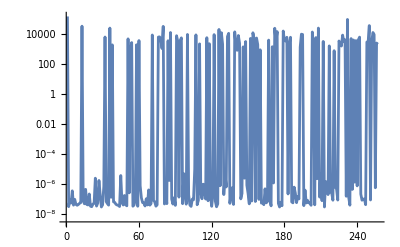

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-24.1809,L2PhaseSet→-36.7555,Q1EkG→159.518,Q2EkG→-153.731,Q3EkG→110.047,Q4EkG→130.372,Q5EkG→-23.4572,Q6EkG→-142.143,S1ELkG→792.723,S2ELkG→-2095.8,S3ELkG→-1021.31,S3ERkG→-1025.77,S2ERkG→-2084.86,S1ERkG→815.415,Q5FFkG→-70.8825,Q4FFkG→-116.862,Q3FFkG→85.2343,Q2FFkG→132.97,Q1FFkG→-247.393,Q0FFkG→166.779,Q0DkG→-109.747,Q1DkG→183.759,Q2DkG→-110.834,PDrive_mean_x→-0.0000655892,PDrive_mean_y→-3.061×10^-7,PDrive_sigma_x→0.0000204429,PDrive_sigma_y→0.0000218857,PDrive_mean_xp→6.8682×10^-6,PDrive_mean_yp→-7.75×10^-7,PDrive_sigmaSI90_x→0.0000194176,PDrive_sigmaSI90_y→0.0000141143,PDrive_emitSI90_x→0.0000844839,PDrive_emitSI90_y→7.2376×10^-6,PDrive_zLen→0.0000218418,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0000586493,PWitness_mean_y→1.0274×10^-6,PWitness_sigma_x→0.0000355721,PWitness_sigma_y→0.0000269354,PWitness_mean_xp→-0.000219659,PWitness_mean_yp→-3.916×10^-7,PWitness_sigmaSI90_x→0.0000309886,PWitness_sigmaSI90_y→0.0000242823,PWitness_emitSI90_x→0.000123978,PWitness_emitSI90_y→9.3508×10^-6,PWitness_zLen→0.0000635076,PWitness_zCentroid→991.332,bunchSpacing→0.0000116757,transverseCentroidOffset→7.0669×10^-6,lostChargeFraction→0.,maximizeMe→137352.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -24.180852462
L2PhaseSet : -36.7554809796
Q1EkG : 159.5177789103
Q2EkG : -153.7313313543
Q3EkG : 110.0473820683
Q4EkG : 130.3719708188
Q5EkG : -23.4571753225
Q6EkG : -142.142961114
S1ELkG : 792.7230326765
S2ELkG : -2095.7968067085
S3ELkG : -1021.3060493766
S3ERkG : -1025.7719740892
S2ERkG : -2084.8581472022
S1ERkG : 815.4147480577
Q5FFkG : -70.8825293872
Q4FFkG : -116.8615871988
Q3FFkG : 85.234262852
Q2FFkG : 132.9700993456
Q1FFkG : -247.3933125558
Q0FFkG : 166.7787740629
Q0DkG : -109.7471192544
Q1DkG : 183.7586118719
Q2DkG : -110.8344328423
PDrive_mean_x : -0.0000655892
PDrive_mean_y : -3.061e-7
PDrive_sigma_x : 0.0000204429
PDrive_sigma_y : 0.0000218857
PDrive_mean_xp : 6.8682e-6
PDrive_mean_yp : -7.75e-7
PDrive_sigmaSI90_x : 0.0000194176
PDrive_sigmaSI90_y : 0.0000141143
PDrive_emitSI90_x : 0.0000844839
PDrive_emitSI90_y : 7.2376e-6
PDrive_zLen : 0.0000218418
PDrive_zCentroid : 991.331770162
PWitness_mean_x : -0.0000586493
PWitness_mean_y : 1.0274e-6
PWitness_sigma_x : 0.0000355721
PWitness_sigma_y : 0.0000269354
PWitness_mean_xp : -0.000219659
PWitness_mean_yp : -3.916e-7
PWitness_sigmaSI90_x : 0.0000309886
PWitness_sigmaSI90_y : 0.0000242823
PWitness_emitSI90_x : 0.0001239778
PWitness_emitSI90_y : 9.3508e-6
PWitness_zLen : 0.0000635076
PWitness_zCentroid : 991.3317818377
bunchSpacing : 0.0000116757
transverseCentroidOffset : 7.0669e-6
lostChargeFraction : 0.
maximizeMe : 137351.539718758

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

7.06685×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1EkG,Q1FFkG,Q2EkG,Q2FFkG,Q3EkG,Q3FFkG,Q4EkG,Q4FFkG,Q5EkG,Q5FFkG,Q6EkG,S1ELkG,S1ERkG,S2ELkG,S2ERkG,S3ELkG,S3ERkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
]
```

FittedModel[…]

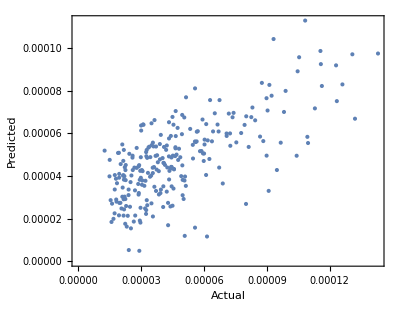

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVars
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{L1PhaseSet→Indeterminate,L2PhaseSet→Indeterminate,Q0FFkG→Indeterminate,Q1EkG→Indeterminate,Q1FFkG→Indeterminate,Q2EkG→Indeterminate,Q2FFkG→Indeterminate,Q3EkG→Indeterminate,Q3FFkG→Indeterminate,Q4EkG→Indeterminate,Q4FFkG→Indeterminate,Q5EkG→Indeterminate,Q5FFkG→Indeterminate,Q6EkG→Indeterminate,S1ELkG→Indeterminate,S1ERkG→Indeterminate,S2ELkG→Indeterminate,S2ERkG→Indeterminate,S3ELkG→Indeterminate,S3ERkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L1PhaseSet | 1 | 4.76622×10^-8 | 4.76622×10^-8 | 116.566 | 2.40443×10^-22
L2PhaseSet | 1 | 1.80986×10^-9 | 1.80986×10^-9 | 4.42631 | 0.0364474
Q0FFkG | 1 | 4.40633×10^-9 | 4.40633×10^-9 | 10.7764 | 0.00118383
Q1EkG | 1 | 6.92031×10^-11 | 6.92031×10^-11 | 0.169248 | 0.681155
Q1FFkG | 1 | 1.41022×10^-10 | 1.41022×10^-10 | 0.344893 | 0.55758
Q2EkG | 1 | 3.12819×10^-10 | 3.12819×10^-10 | 0.765051 | 0.382642
Q2FFkG | 1 | 8.91221×10^-10 | 8.91221×10^-10 | 2.17963 | 0.141181
Q3EkG | 1 | 1.39014×10^-8 | 1.39014×10^-8 | 33.9983 | 1.8036×10^-8
Q3FFkG | 1 | 5.64329×10^-11 | 5.64329×10^-11 | 0.138016 | 0.710595
Q4EkG | 1 | 1.12446×10^-8 | 1.12446×10^-8 | 27.5006 | 3.48876×10^-7
Q4FFkG | 1 | 1.2792×10^-9 | 1.2792×10^-9 | 3.12851 | 0.0782259
Q5EkG | 1 | 2.09877×10^-10 | 2.09877×10^-10 | 0.51329 | 0.474426
Q5FFkG | 1 | 8.60353×10^-11 | 8.60353×10^-11 | 0.210414 | 0.646865
Q6EkG | 1 | 9.82338×10^-10 | 9.82338×10^-10 | 2.40247 | 0.122484
S1ELkG | 1 | 1.10003×10^-9 | 1.10003×10^-9 | 2.69032 | 0.102292
S1ERkG | 1 | 5.8253×10^-11 | 5.8253×10^-11 | 0.142467 | 0.70618
S2ELkG | 1 | 3.08536×10^-11 | 3.08536×10^-11 | 0.0754576 | 0.783791
S2ERkG | 1 | 7.146×10^-11 | 7.146×10^-11 | 0.174767 | 0.676289
S3ELkG | 1 | 1.05612×10^-11 | 1.05612×10^-11 | 0.0258292 | 0.872456
S3ERkG | 1 | 3.52574×10^-9 | 3.52574×10^-9 | 8.62278 | 0.00364819
Error | 236 | 9.64972×10^-8 | 4.08886×10^-10 |  | 
Total | 256 | 1.84347×10^-7 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVars,
Symbol[#]&/@freeVars
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

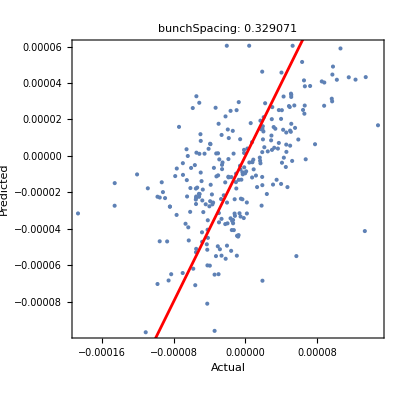
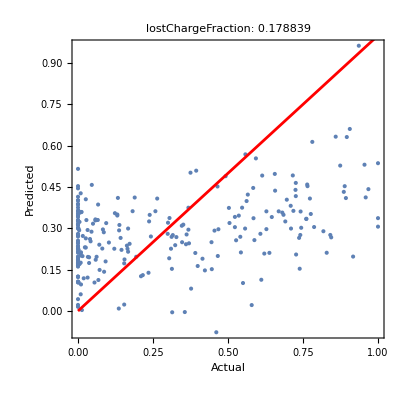
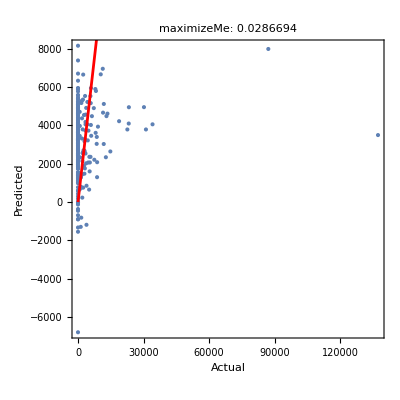
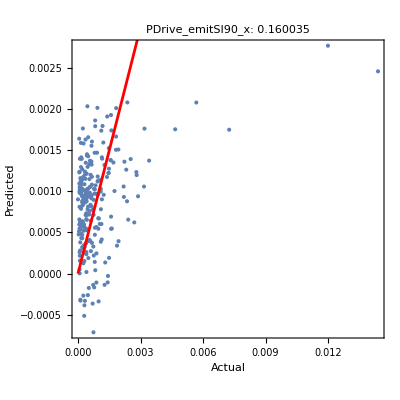
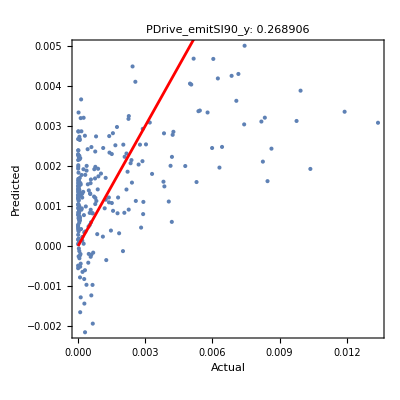
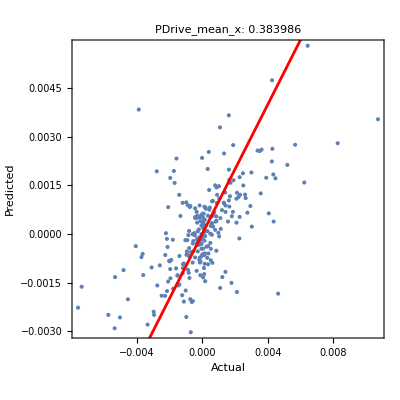
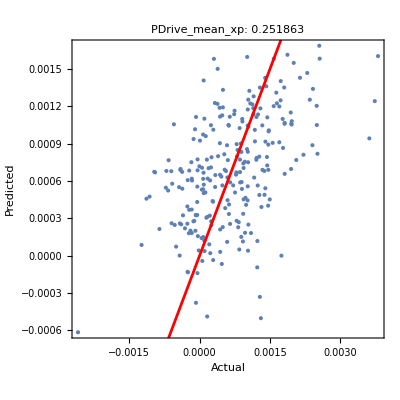
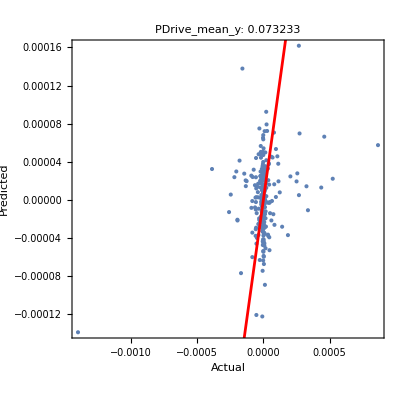
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 0

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```